## Q3)

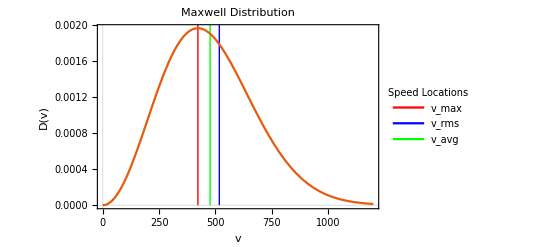

```mathematica
v0=√((2*1.3806488*10^-23*300)/(28.02*1.660538921*10^-27));
MD[v_]:=4/(√π)*v^2/v0^3*Exp[-v^2/v0^2];
Plot[MD[v],{v,0,1200},PlotTheme->"Scientific",FrameLabel->{"v","D(v)
"},Prolog->{Red,Line[{{422,0},{422,1}}],Blue,Line[{{517,0},{517,1}}],Green,Line[{{476,0},{476,1}}]},PlotLabel->"Maxwell Distribution",PlotLegends->Placed[LineLegend[{Red,Blue,Green},{"v_max","v_rms","v_avg"},LegendLabel->"Speed Locations",LegendLayout->{"Column",2}],{0.8,0.7}]
]
```

```mathematica
Integrate[MD[v],{v,300,572}]
```

0.499873

## Q5)

## a) & b)

```mathematica
mq1[q_]:=Binomial[200+200-q,200-q]/Binomial[200+200,200]
```

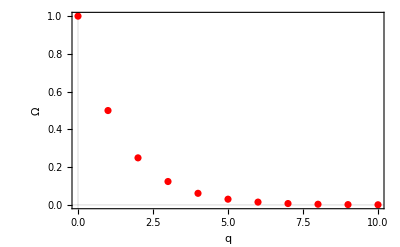

```mathematica
ListPlot[Table[mq1[q],{q,0,10}],PlotTheme->"Scientific",FrameLabel->{"q","Ω
"},DataRange->{0,10},PlotStyle->Red,PlotRange->All]
```

```mathematica
FindFit[Table[mq1[q],{q,0,10}], a*Exp[-q/b],{a,b},q]
```

{a→2.00389,b→1.43923}

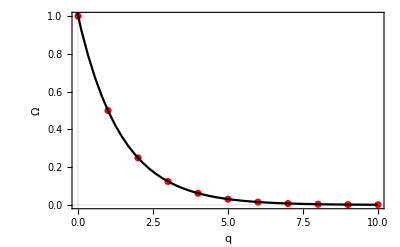

```mathematica
Show[ListPlot[Table[mq1[q],{q,0,10}],PlotStyle->Red,PlotTheme->"Scientific",FrameLabel->{"q","Ω
"},DataRange->{0,10}],Plot[a Exp[-(q+1)/b]/.{a->2.0038898158801857,b->1.4392349384490526},{q,-1,10},PlotStyle->Black]]
```

## d)

```mathematica
mq2[q_]:=Binomial[2000+200-q,2000-q]/Binomial[2000+200,2000]
```

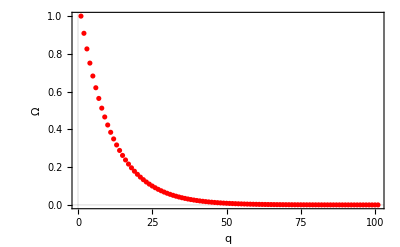

```mathematica
ListPlot[Table[mq2[q],{q,0,100}],PlotTheme->"Scientific",FrameLabel->{"q","Ω
"},PlotStyle->Red,PlotRange->All]
```

```mathematica
FindFit[Table[mq2[q],{q,0,100}],a*Exp[-q/b],{a,b},q]
```

{a→1.10161,b→10.4446}

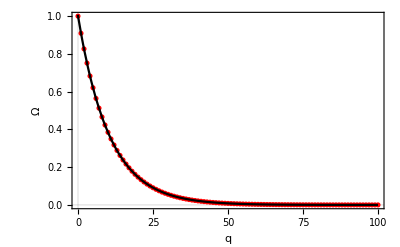

```mathematica
Show[ListPlot[Table[mq2[q],{q,0,100}],PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",FrameLabel->{"q","Ω
"},DataRange->{0,100}],Plot[a Exp[-(q+1)/b]/.{a->1.1016088444611236,b->10.444575609529062},{q,-10,100},PlotStyle->Black]]
```